

```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_3TeV_fix.txt"];
interZP = Get["intang_ZPtt_3TeV_fix.txt"];
interZPPP = Get["intang_ZPPPtt_3TeV.txt"];
interZPZZ = Get["intang_ZPZZtt_3TeV.txt"];
interPPZZ = Get["intang_PPZZtt_3TeV.txt"];
interZPPZ= Get["intang_ZPPZtt_3TeV.txt"];
```

```mathematica
interWW = Get["intang_WWtt1_3TeV.txt"];
interZZ = Get["intang_ZZtt_3TeV_Fix.txt"];
```

```mathematica
dytinterWW = Get["intang_WWttDYT_10TeV_3.txt"];
dytinterWW11= Get["intang_WWttDYT11_10TeV_3.txt"];
dytinterWWm1m1= Get["intang_WWttDYTm1m1_10TeV_3.txt"];
dytinterZZ = Get["intang_ZZtt00DYT_10TeV_3_new.txt"];
dytinterZZ11= Get["intang_ZZtt11DYT_10TeV_3.txt"];
dytinterZZm1m1= Get["intang_ZZttm1m1DYT_10TeV_3.txt"];
dytt = Table[(1/1000)*(20i-200),{i,0,20}]
```

Get::noopen: Cannot open intang_WWttDYT_10TeV_3.txt.

Get::noopen: Cannot open intang_WWttDYT11_10TeV_3.txt.

Get::noopen: Cannot open intang_WWttDYTm1m1_10TeV_3.txt.

Get::noopen: Cannot open intang_ZZtt00DYT_10TeV_3_new.txt.

Get::noopen: Cannot open intang_ZZtt11DYT_10TeV_3.txt.

Get::noopen: Cannot open intang_ZZttm1m1DYT_10TeV_3.txt.

{-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5}

```mathematica
dytt[[11]]
```

0

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]

angenZPPP[ang_,num_] :=interZPPP[[ang]][(1 + ((num - 350)/50))]

angenZPZZ[ang_,num_] :=interZPZZ[[ang]][(1 + ((num - 350)/50))]

angenPPZZ[ang_,num_] :=interPPZZ[[ang]][(1 + ((num - 350)/50))]

angenZPPZ[ang_,num_] :=interZPPZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
isumWWdyt[ang_,dyt_,energy_] :=dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11[ang_,dyt_,energy_] :=dytinterWW11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1[ang_,dyt_,energy_] :=dytinterWWm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt00[ang_,dyt_,energy_] :=dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt11[ang_,dyt_,energy_] :=dytinterZZ11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdytm1m1[ang_,dyt_,energy_] :=dytinterZZm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
lum = 1;
sqrtsbin = Table[350 + 50*i, {i,0,54}];
```

```mathematica
PP = Table[Sum[angenPP[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
ZP = Table[Sum[angenZP[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
WW = Table[Sum[angenWW[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
ZZ= Table[Sum[angenZZ[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
ZPPP= Table[Sum[angenZPPP[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
ZPZZ= Table[Sum[angenZPZZ[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
PPZZ= Table[Sum[angenPPZZ[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
ZPPZ= Table[Sum[angenZPPZ[k,sqrtsbin [[i]]],{k,1,18}],{i,1,Length@sqrtsbin}];
```

```mathematica
sqrtsbin1 = Table[350 + 10*i, {i,0,265}];
```

```mathematica
PP1 = Table[{sqrtsbin [[k]],PP[[k]]},{k,1,Length@sqrtsbin}];
intPP = Interpolation[PP1 ]

ZP1 = Table[{sqrtsbin [[k]],ZP[[k]]},{k,1,Length@sqrtsbin}];
intZP = Interpolation[ZP1 ]

WW1 = Table[{sqrtsbin [[k]],WW[[k]]},{k,1,Length@sqrtsbin}];
intWW = Interpolation[WW1 ]

ZZ1 = Table[{sqrtsbin [[k]],ZZ[[k]]},{k,1,Length@sqrtsbin}];
intZZ = Interpolation[ZZ1 ]

ZPPP1 = Table[{sqrtsbin [[k]],ZPPP[[k]]},{k,1,Length@sqrtsbin}];
intZPPP = Interpolation[ZPPP1 ]

ZPZZ1 = Table[{sqrtsbin [[k]],ZPZZ[[k]]},{k,1,Length@sqrtsbin}];
intZPZZ = Interpolation[ZPZZ1 ]

PPZZ1 = Table[{sqrtsbin [[k]],PPZZ[[k]]},{k,1,Length@sqrtsbin}];
intPPZZ = Interpolation[PPZZ1 ]

ZPPZ1 = Table[{sqrtsbin [[k]],ZPPZ[[k]]},{k,1,Length@sqrtsbin}];
intZPPZ = Interpolation[ZPPZ1 ]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«5 more identical outputs»

```mathematica
WWDYT1 = Table[{sqrtsbin [[k]],WW[[k]]+WWDYT [[k]]},{k,1,Length@sqrtsbin}];
intWWDYT = Interpolation[WWDYT1]
```

Part::partd: Part specification WWDYT⟦1⟧ is longer than depth of object.

Part::partd: Part specification WWDYT⟦2⟧ is longer than depth of object.

Part::partd: Part specification WWDYT⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
ZZDYT1 = Table[{sqrtsbin [[k]],ZZ[[k]]+ZZDYT [[k]]},{k,1,Length@sqrtsbin}];
intZZDYT = Interpolation[ZZDYT1]
```

Part::partd: Part specification ZZDYT⟦1⟧ is longer than depth of object.

Part::partd: Part specification ZZDYT⟦2⟧ is longer than depth of object.

Part::partd: Part specification ZZDYT⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ticks0=LogTicks[10,-3,6,TickLabelStep->1];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1[[7,1]]
```

1000.

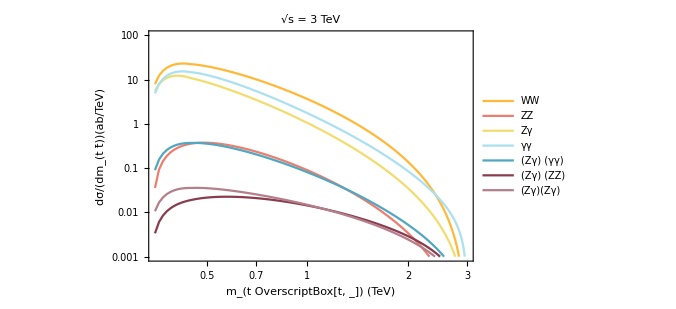

```mathematica
lineplot=ListLogLogPlot[{Transpose[{sqrtsbin1/1000,intWW[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,intZZ[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,2 intZP[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,intPP[sqrtsbin1]}], Transpose[{sqrtsbin1/1000,4 intZPPP[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,4 intZPZZ[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,(2 intPPZZ[sqrtsbin1]+2 intZPPZ[sqrtsbin1])}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][5],ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][8]},Frame->True,FrameLabel->{Style[DisplayForm["m_(t OverscriptBox[t, _]) (TeV)"],Black,26,FontFamily->"Times"],Style[DisplayForm["dσ/(dm_(t t̄))(ab/TeV)"],Black,26,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,30,FontFamily->"Times"],
PlotLegends->{Style[" WW ",Black,20,FontFamily->"Times"],Style[" ZZ ",Black,20,FontFamily->"Times"],Style[" Zγ ",Black,20,FontFamily->"Times"],Style[" γγ ",Black,20,FontFamily->"Times"],Style[" (Zγ) (γγ) ",Black,20,FontFamily->"Times"],Style[" (Zγ) (ZZ) ",Black,20,FontFamily->"Times"],Style[" (Zγ)(Zγ) ",Black,20,FontFamily->"Times"]},
PlotRange->{{.350,3},{0.001,100}},FrameTicks->{{ticks1,Automatic},{{.500,1,2,3},Automatic}},
FrameTicksStyle->Directive[Black,18],ImageSize->500]
```

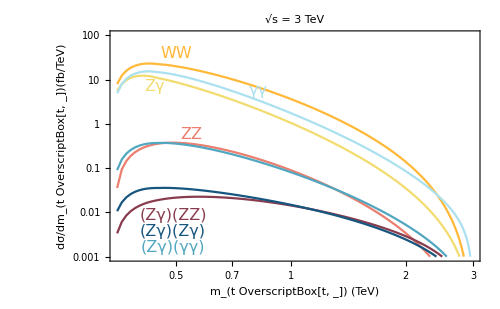

```mathematica
lineplot=ListLogLogPlot[{Transpose[{sqrtsbin1/1000,intWW[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,intZZ[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,2 intZP[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,intPP[sqrtsbin1]}], Transpose[{sqrtsbin1/1000,4 intZPPP[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,4 intZPZZ[sqrtsbin1]}],Transpose[{sqrtsbin1/1000,(2 intPPZZ[sqrtsbin1]+2 intZPPZ[sqrtsbin1])}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][5],ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][7]},Frame->True,FrameLabel->{Style[DisplayForm["m_(t OverscriptBox[t, _]) (TeV)"],Black,18,FontFamily->"Times"],Style[DisplayForm["dσ/dm_(t OverscriptBox[t, _])(fb/TeV)"],Black,16,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",3 TeV}]  ,Black,18,FontFamily->"Times"],
(*PlotLegends->{Style[" WW ",Black,20,FontFamily->"Times"],Style[" ZZ ",Black,20,FontFamily->"Times"],Style[" Zγ ",Black,20,FontFamily->"Times"],Style[" γγ ",Black,20,FontFamily->"Times"],Style[" (Zγ) (γγ) ",Black,20,FontFamily->"Times"],Style[" (Zγ) (ZZ) ",Black,20,FontFamily->"Times"],Style[" (Zγ)(Zγ) ",Black,20,FontFamily->"Times"]},*)
Epilog->{Inset[Style["WW",ColorData[colorselecitonumber][2],16,FontFamily->"Times"],Scaled[{0.18,0.90}]],
Inset[Style["ZZ",ColorData[colorselecitonumber][1],16,FontFamily->"Times"],Scaled[{0.22,0.55}]],Inset[Style["Zγ",ColorData[colorselecitonumber][3],16,FontFamily->"Times"],Scaled[{0.12,0.76}]],Inset[Style["γγ",ColorData[colorselecitonumber][4],16,FontFamily->"Times"],Scaled[{0.40,0.74}]],Inset[Style[" (Zγ)(γγ)",ColorData[colorselecitonumber][5],16,FontFamily->"Times"],Scaled[{0.17,0.06}]],Inset[Style[" (Zγ)(ZZ)",ColorData[colorselecitonumber][9],16,FontFamily->"Times"],Scaled[{0.17,0.20}]],Inset[Style[" (Zγ)(Zγ)",ColorData[colorselecitonumber][7],16,FontFamily->"Times"],Scaled[{0.17,0.13}]]},
PlotRange->{{.350,3},{0.001,100}},FrameTicks->{{ticks1,Automatic},{{.500,1,2,3},Automatic}},
FrameTicksStyle->Directive[Black,18],ImageSize->500]
```

```mathematica
Export["Convolute_PDF_3TeV_interference.pdf",lineplot]
```

Convolute_PDF_3TeV_interference.pdf